# Лабораторная работа №1

## Математические модели динамики численности популяции одного вида

Мат. моделирование динамических процессов 1
БГУ, ММФ, 3 курс, 6 семестр
специальность Компьютерная математика и системный анализ
февраль 2022
доц. Лаврова О.А., доц. Щеглова Н.Л.
работу выполнил 
студент 3 курса 5 группы ММФ БГУ
Кирилло Дмитрий

## Задание 1. Модель Мальтуса

Модель Мальтуса, или модель экспоненциального роста (1798) является одной из простейших моделей численности популяции одного вида. Модель была предложена Мальтусом для описания роста численности населения Земли.

### Содержательная постановка задачи

Рассмотрим популяцию больших размеров, численность которой измеряется миллионами и более. Полагаем, что не существует факторов, сдерживающих рост популяции (болезни, хищники, конкурирующие виды, ограниченность питания). Игнорируем процессы иммиграции и эмиграции. Необходимо определить изменение численности популяции во времени.

### Концептуальная постановка задачи

Численность популяции рассматривается как непрерывная функция времени N=N(t). В силу того, что популяция достаточно велика, игнорируем случайные различия между отдельными особями. Полагаем, что каждая особь в популяции имеет равные шансы родить и умереть в течение определенного промежутка времени. Полагаем, что рождаемость и смертность непрерывны во времени и заданы коэффициентами рождаемости α(t)≥0 и смертности β(t)≥0 на одну особь в единицу времени.

В основу модели Мальтуса положено утверждение, что скорость изменения численности популяции N'(t) пропорциональна ее текущей численности N(t) в момент времени t, с коэффициентом пропорциональности, равным разности коэффициентов рождаемости и смертности

N'(t)==(α(t)-β(t))N(t).

Предположение вида “скорость изменения величины пропорциональна значению самой величины (или некоторой функции от нее)” широко используется в различных областях знаний.

Модель Мальтуса является примером применения принципа аналогии при построении математических моделей объектов, для которых невозможно указать фундаментальные законы или вариационные принципы, которым они подчиняются.

### Математическая модель

Моделью Мальтуса называется задача Коши для уравнения (1) при заданном начальном условии в момент времени t=t_0

N'(t)==(α(t)-β(t)) N(t),
N(t_0)=N_0.

### Задание 1.1 (аналитическое решение)

Постройте аналитическое решение модели Мальтуса (2), например, методом разделения переменных для заданной численности населения N_0 в начальный момент времени t_0. Сравните построенное решение  и решение, полученное с помощью функции DSolve

```mathematica
ClearAll[t0,N0];
sol=DSolveValue[{NN'[t]==(α[t]-β[t]) NN[t],NN[t0]==N0},NN[t],t]
```

ⅇ^((α[K[1]]-β[K[1]])K[1]1t-(α[K[1]]-β[K[1]])K[1]1t0) N0

Напишите пользовательскую функцию для задания аналитического решения модели Мальтуса, где α(t), β(t) и N_0≥0 и t_0≥ 0 являются аргументами функции.

Piecewise[{{N'(t)==(α(t)-β(t)) N(t), ,}, {N(t_0)=N_0, .}}]

Решение
(d OverTilde[N(τ)])/dτ=(α(τ)-β(τ)) OverTilde[N(τ)];
(dÑ(τ))/OverTilde[N(τ)]=(α(τ)-β(τ))dτ;
∫_N0^N (ⅆ OverTilde[N(τ)])/OverTilde[N(τ)]=∫_t0^t (α(τ)-β(τ))dτ;
ln(|OverTilde[N(τ)]|)|_N0^N=∫_t0^t (α(τ)-β(τ))dτ;
N/N0=e^(∫_t0^t (α(τ)-β(τ))dτ);
N= e^(∫_t0^t (α(τ)-β(τ))dτ)N0;

```mathematica
ClearAll[MaltusModel];
MaltusModel[N0_,t0_,t_]:=ⅇ^Integrate[α[τ]-β[τ],{τ,t0,t}] N0;
```

### Задание 1.2 (график аналитического решения)

Изобразите в одной системе координат графики функции N(t) для фиксированных значений t_0 и N_0>0 и различных значений α(t)=α_0=const и β(t)=β_0=const. Рассмотрите случаи α_0<β_0, α_0=β_0, α_0>β_0.

Пример построения графиков решений

```mathematica
t0=1; N0=10;
```

```mathematica
funcs = (Activate@(sol/.#))&/@{{α[_]->0,β[_]->2},{α[_]->2,β[_]->2},{α[_]->2,β[_]->0}}
```

{10 ⅇ^(-2 (-1+t)),10,10 ⅇ^(2 (-1+t))}

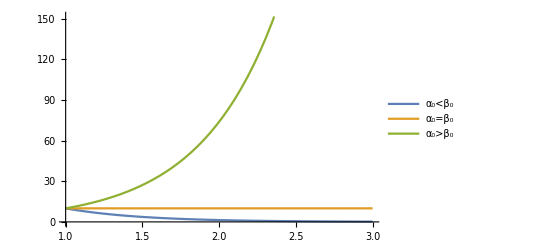

```mathematica
Plot[funcs,{t,t0,3},PlotLegends->{"α_0<β_0","α_0=β_0","α_0>β_0"}]
```

При выполнении задания необходимо использовать пользовательскую функцию из Задания 1.1 для описания аналитического решения модели Мальтуса.

```mathematica
(MaltusModel[N0,t0,t]/.#)&/@{{α[_]->0,β[_]->2},{α[_]->2,β[_]->2},{α[_]->2,β[_]->0}}
```

{10 ⅇ^(-2 (-1+t)),10,10 ⅇ^(2 (-1+t))}

```mathematica
MaltusFunction=(MaltusModel[N0,t0,t]/.#)&/@{{α[_]->0,β[_]->2},{α[_]->2,β[_]->2},{α[_]->2,β[_]->0}}
```

{10 ⅇ^(-2 (-1+t)),10,10 ⅇ^(2 (-1+t))}

```mathematica
Plot[MaltusFunction,{t,t0,3},PlotLegends->{"α_0<β_0","α_0=β_0","α_0>β_0"}]
```

-Graphics-

### Задание 1.3 (качественный анализ модели по решению)

На основании построенных графиков в Задании 1.2 сформулируйте выводы о поведении решения модели Мальтуса при t→∞ для случаев α_0<β_0, α_0=β_0, α_0>β_0 (например, монотонное возрастание/убывание, экспоненциальное возрастание/убывание, колебания, экспоненциальный рост, гиперболический рост). Определите, является ли положение равновесия N(t)≡N_0, соответствующее решению модели при совпадении коэффициентов рождаемости и смертности α_0=β_0, устойчивым относительно изменения значений параметров α_0,β_0?

```mathematica
Manipulate[{{"α="Dynamic[α1],"β="Dynamic[β1],"N_0="Dynamic[N01],"t_0="Dynamic[t01],"t_1="Dynamic[t01+t11]},Plot[(MaltusModel[N01,t01,t]/.#)&/@{{α[_]->α1,β[_]->β1}},{t,t01,t01+t11},PlotRange->20,ImageSize->{{500,20}}]},
{{α1,1},0,2,0.01},
{{β1,1},0,2,0.01},
{{N01,1,"N_0"},1, 10}, 
{{t01,0,"t_0"}, 0, 10},
{{t11,1,"t_1"},1,10}]
```

```mathematica
Manipulate[{{"α="Dynamic[α],"β="Dynamic[β],"N_0="Dynamic[N0],"t_0="Dynamic[t0],"t_1="Dynamic[t0+t1]},Plot[ⅇ^((α-β)(t-t0))N0 ,{t,t0,t0+t1},PlotRange->20,ImageSize->{{500,20}}]},
{{α,1},0,2,0.01},
{{β,1},0,2,0.01},
{{N0,1,"N_0"},1, 10}, 
{{t0,0,"t_0"}, 0, 10},
{{t1,1,"t_1"},1,10}]
```

Вывод: как можно заметить из изменения данных, при α_0<β_0 график модели экспоненциально убывает и, как можно заметить, стремится к приближению по оси ОХ к 0. При α_0=β_0  принимает постоянную модель или, в нашем случае, положение равновесия. При α_0>β_0 график модели экспоненциально возрастает. 
Положение равновесия при N(t)≡N_0, соответствующее решению модели при совпадении коэффициентов рождаемости и смертности α_0=β_0, не является устойчивым при относительном изменения значений параметров α_0,β_0

### Задание 1.4 (качественный анализ модели по фазовому портрету)

Фазовое пространство для рассматриваемой динамической системы первого порядка является одномерным и представляет собой прямую линию ON, которая ограничена значениями N≥0 в силу того, что N(t) является численностью населения. 

Изобразите фазовые траектории (например, с помощью функции StreamPlot) решений динамической системы для случая постоянных коэффициентов α(t)=α_0=const и β(t)=β_0=const при α_0<β_0, α_0=β_0, α_0>β_0 . Пользуясь определением устойчивости в фазовом пространстве выясните, являются ли положения равновесия динамической системы устойчивыми при условии, что N(t)≥0.

Например,

```mathematica
α=1; β=2;
```

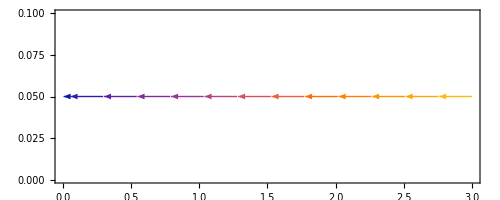

```mathematica
StreamPlot[{(α-β)x,0},{x,0,3},{y,0,.1},AspectRatio->Automatic,ImageSize->{{500,20}}]
```

```mathematica
Manipulate[{{"α=",Dynamic[α],"β=",Dynamic[β]},StreamPlot[{x(α-β),0},{x,0,5},{y,0,.2},AspectRatio->Automatic,ImageSize->{{700,10}}]},
{{α,1},0,2,0.01},{{β,1.1},0,2,0.01}]
```

Вывод: как можно заметить из фазовых траекторий модели, динамическая система является устойчивой при α_0<β_0, а также при α_0=β_0. Также мы можем увидеть,что динамическая система модели является устойчивой при значении х = 0. В остальных случаях, в частности, при α_0>β_0  динамическая система модели не устойчива

## Задание 2. Логистическая модель или модель Ферхюльста

### Содержательная постановка задачи

Рассмотрим популяцию больших размеров, численность которой измеряется миллионами и более. Полагаем, что сдерживающим фактором роста популяции является ограниченность ресурсов. Игнорируем процессы иммиграции и эмиграции. Необходимо определить изменение численности популяции во времени.

### Концептуальная постановка задачи и математическая модель

Логистическая модель или модель Ферхюльста (1838, 1845) принимает во внимание ограниченность доступных популяции ресурсов. В частности, считается, что существует равновесная численность популяции N_p=const>0, которую может обеспечить окружающая среда, т.е. N(t)→N_p при t→∞. Это свойство называется эффектом насыщения численности населения.
 
При моделировании полагается также, что скорость изменения численности популяции пропорциональна самой численности, умноженной (в отличие от модели Мальтуса) на величину ее отклонения от равновесного значения N_p

N'(t)==N(t) k(1-(N(t))/N_p),             k=const>0.

Логистической моделью называется задача Коши для уравнения (3) при заданном начальном условии в момент времени t=t_0

N'(t)==N(t)k(1-(N(t))/N_p),
N(t_0)=N_0.

Предположение о механизмах насыщения используются при построении многих моделей в различных областях знаний.

Существенным недостатком математической модели является тот факт, что равновесная численность популяции N_p вводится в качестве известного параметра, в то время как нахождение этой величины нередко является основной задачей исследования.

Современные прогнозы показывают, что численность человечества в обозримом будущем стабилизируется на уровне N_p=12*10^9 человек. Такой же прогноз дается ООН.

### Задание 2.1 (аналитическое решение)

Постройте аналитическое решение логистической модели (4) (например, методом разделения переменных) для заданной численности населения N_0 в начальный момент времени t_0. 
Сравните построенное решение  и решение, полученное с помощью функции DSolve. 
Напишите пользовательскую функцию для задания аналитического решения логистической модели, где k>0, N_p>0, N_0≥0 и t_0≥ 0  являются аргументами функции.

```mathematica
ClearAll[t0,N0];
solFerhust=DSolve[{NN'[t]==NN[t] k(1-NN[t]/Np),NN[t0]==N0},NN[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{NN[t]→(ⅇ^(k t) N0 Np)/(ⅇ^(k t) N0-ⅇ^(k t0) N0+ⅇ^(k t0) Np)}}

```mathematica
ClearAll[FerhustModel];
FerhustModel[k_,Np_,N0_,t0_,t_]:=Module[{ans},
If[k≤0||Np≤0||N0<0||t0<0||t0> t,Return["Error in entered data"]];
Return[(N0 Np ⅇ^(k(t-t0)))/(N0(ⅇ^(k (t-t0))-1)+Np)];
];
```

```mathematica
Evaluate[(NN[t]/.First@First@solFerhust)/.{{N0->1},{N0->10},{N0->15}}]
```

{(ⅇ^(k t) Np)/(ⅇ^(k t)-ⅇ^(k t0)+ⅇ^(k t0) Np),(10 ⅇ^(k t) Np)/(10 ⅇ^(k t)-10 ⅇ^(k t0)+ⅇ^(k t0) Np),(15 ⅇ^(k t) Np)/(15 ⅇ^(k t)-15 ⅇ^(k t0)+ⅇ^(k t0) Np)}

```mathematica
FerhustModel[k,Np,N0,t0,t1]/.{{N0->1},{N0->12},{N0->15}}
```

{(ⅇ^(k (-t0+t1)) Np)/(-1+ⅇ^(k (-t0+t1))+Np),(12 ⅇ^(k (-t0+t1)) Np)/(12 (-1+ⅇ^(k (-t0+t1)))+Np),(15 ⅇ^(k (-t0+t1)) Np)/(15 (-1+ⅇ^(k (-t0+t1)))+Np)}

### Задание 2.2 (график аналитического решения)

Изобразите в одной системе координат графики функции N(t) для фиксированных значений k, N_p и t_0 и различных значений N_0. Рассмотрите случаи, когда  N_0<N_p, N_0=N_p, N_0>N_p. При выполнении задания необходимо использовать пользовательскую функцию из Задания 2.1 для описания аналитического решения логистической модели.

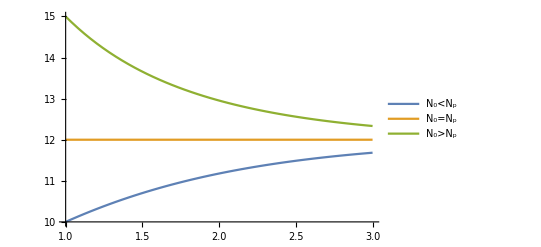

```mathematica
ClearAll[k,N0,Np,t0,t1];
k=1;
Np=12;
t0=1;
t1=3;
Plot[Evaluate[(NN[t]/.solFerhust⟦1,1⟧)/.{{N0->10},{N0->12},{N0->15}}],{t,t0,t1},PlotLegends->{"N_0<N_p","N_0=N_p","N_0>N_p"}]
ClearAll[k,N0,Np,t0,t1];
```

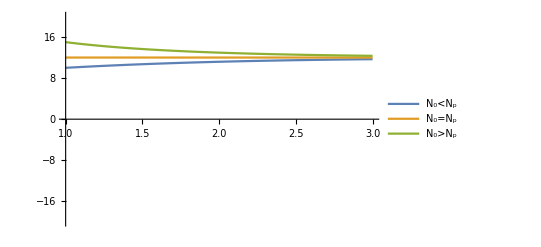

```mathematica
ClearAll[k,N0,Np,t0,t1];
k=1;
Np=12;
t0=1;
t1=3;
Plot[{(FerhustModel[k,Np,N0,t0,t])/.{N0->10},(FerhustModel[k,Np,N0,t0,t])/.{N0->12},(FerhustModel[k,Np,N0,t0,t])/.{N0->15}},{t,t0,t1},PlotLegends->{"N_0<N_p","N_0=N_p","N_0>N_p"},PlotRange->20]
ClearAll[k,N0,Np,t0,t1];
```

### Задание 2.3 (качественный анализ модели по решению)

На основании построенных графиков в Задании 2.2 сформулируйте выводы о поведении решения логистической модели при t→∞ для случаев N_0<N_p, N_0=N_p, N_0>N_p при k>0. Определите, является ли положение равновесия N(t)≡N_p, соответствующее решению модели при N_0=N_p, устойчивым по начальным данным?

```mathematica
Manipulate[{{"k="Dynamic[k],"N_p="Dynamic[Np],"N_0="Dynamic[N0],"t_0="Dynamic[t0],"t_1="Dynamic[t0+t1]},Plot[FerhustModel[k,Np,N0,t0,t],{t,t0,t0+t1},PlotRange->20,ImageSize->{{500,20}}]},
{{k,1},0.1,2,0.01},
{{Np,1},0.1,2,0.01},
{{N0,1,"N_0"},0, 10}, 
{{t0,0,"t_0"}, 0, 10},
{{t1,1,"t_1"},1,10}]
```

Вывод: как можно заметить из изменения данных, при k>0, а также при N_0<N_p и  N_0>N_p график модели стремится к положению равновесия, то есть стремится к модели при коэффициентах N_0=N_p .
Положение равновесия N(t)≡N_p, соответствующее решению модели при N_0=N_p, является устойчивым по начальным данным

### Задание 2.4 (качественный анализ модели по фазовому портрету)

Фазовое пространство для рассматриваемой динамической системы первого порядка является одномерным и представляет собой прямую линию ON, которая ограничена значениями N≥0 в силу того, что N(t) является численностью населения. 

Изобразите фазовые траектории решений динамической системы, например, с помощью функции StreamPlot. Пользуясь определением устойчивости в фазовом пространстве выясните, являются ли положения равновесия динамической системы устойчивыми при условии, что k>0, N(t)≥0.

```mathematica
ClearAll[Np,k];
Manipulate[{{"k="Dynamic[k],"N_p="Dynamic[Np]},StreamPlot[{x k(1-x/Np),0},{x,0,5},{y,0,.2},AspectRatio->Automatic,ImageSize->{{700,10}}]},
{{k,0.5},0.1,2,0.1},
{{Np,1},0.1,2,0.1}]
```

Вывод: как можно заметить из фазовых траекторий модели, динамическая система является устойчивой при x= 0  и x= Np, параметр k>0 влияет только на смещение фазовых траекторий модели. То есть, положение равновесия динамической системы является устойчивыми при условии, что k>0, N(t)≥0.

## Задание 3. Нелинейный аналог модели Мальтуса

### Математическая модель

Полагаем, что коэффициент рождаемости пропорционален численности населения (например, потому что особи популяции заинтересованы в ее росте) α(N)=α_0 N, α_0=const>0, а коэффициент смертности постоянный β(t)=β_0=const>0. Тогда уравнение Мальтуса (1) преобразуется к виду

N'(t)==N(t) (α_0 N(t)-β_0)

с квадратичной нелинейностью в правой части.

Математической моделью называется задача Коши для уравнения (5) при заданном начальном условии в момент времени t=t_0

N'(t)==N(t)(α_0 N(t)-β_0),
N(t_0)=N_0.

### Задание 3.1 (аналитическое решение)

Постройте аналитическое решение нелинейной модели (6) для заданной численности населения N_0 в начальный момент времени t_0. При построении аналитического решения необходимо отдельно рассматривать случаи N_0<N_кр, N_0=N_кр, N_0>N_кр, где N_кр=β_0/α_0. При N_0>N_кр решение строится только на отрезке [t_0,t^*], где t^* определяется из условия lim_(t→t^*) N[t]=+∞. 
Сравните построенное решение  и решение, полученное с помощью функции DSolve. 
Напишите пользовательскую функцию для задания аналитического решения нелинейной модели Мальтуса, где N_кр>0, β_0>0, N_0≥0 и t_0≥ 0 являются аргументами функции.

```mathematica
ClearAll[N0,t0,α0,β0 ];
ModelNonLinearMaltus=DSolve[{NN'[t]==NN[t](α0 NN[t]-β0),NN[t0]==N0},NN[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{NN[t]→(ⅇ^(t0 β0) N0 β0)/(-ⅇ^(t β0) N0 α0+ⅇ^(t0 β0) N0 α0+ⅇ^(t β0) β0)}}

```mathematica
Solve[-ⅇ^(t β0) N0 α0+ⅇ^(t0 β0) N0 α0+ⅇ^(t β0) β0==0,t](*tStar how Wolfram Calculate*)
```

{{t→ConditionalExpression[(2 ⅈ π C[1]+Log[(ⅇ^(t0 β0) N0 α0)/(N0 α0-β0)])/β0, C[1]∈ℤ]}}

```mathematica
ClearAll[NonLinearMaltus];
NonLinearMaltus[α_,β_,N0_,t0_,t_]:= Module[{Nkr=β/α},If[Nkr >0&&β>0&&N0≥ 0&&t0≥ 0,Return[(Nkr N0)/(N0-(ⅇ^(β (t-t0)) (N0-Nkr)))],Return["Error in inputed data"]]]
```

```mathematica
NonLinearMaltus[1,1,2,0,3]
```

2/(2-ⅇ^3)

t^*=(ln(N0/(N0-Nk)))/β+t0 (*how I find*)

### Задание 3.2 (график аналитического решения)

Изобразите в одной системе координат графики функции N(t) для фиксированных значений α_0 и β_0 и различных значений N_0. Рассмотрите случаи N_0<N_кр, N_0=N_кр, N_0>N_кр, где N_кр=β_0/α_0. При выполнении задания необходимо использовать пользовательскую функцию из Задания 3.1 для описания аналитического решения нелинейной модели Мальтуса.

ВНИМАНИЕ!!!
Вольфрам может выдавать ошибки при построении графика, так как значение t^* может принимать как комплексное, так и не разрешимое значение, то есть const/0(это связано с тем, что мы рассматриваем случай N_0=N_кр). В конечном случае, график построиться правильно так, как и должно быть

Power::infy: Infinite expression 1/0 encountered.

Plot::plln: Limiting value -0.405465+3.14159 ⅈ in {t,0,-0.405465+3.14159 ⅈ} is not a machine-sized real number.

Plot::plld: Endpoints for t in {t,0,0} must have distinct machine-precision numerical values.

Plot::plln: Limiting value -0.405465+3.14159 ⅈ in {t,0,-0.405465+3.14159 ⅈ} is not a machine-sized real number.

Plot::plld: Endpoints for t in {t,0,0} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

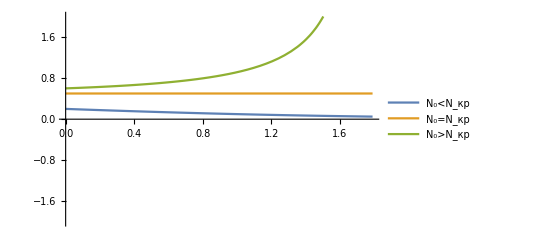
{Plot[{0.2/(0.4+0.6 ⅇ^t),1/2,0.6/(1.2-0.2 ⅇ^t)},{t,t0,tStar⟦1⟧},PlotLegends→{N_0<N_кр,N_0=N_кр,N_0>N_кр},PlotRange→2,ImageSize→{{700,20}}],Plot[{0.2/(0.4+0.6 ⅇ^t),1/2,0.6/(1.2-0.2 ⅇ^t)},{t,t0,tStar⟦2⟧},PlotLegends→{N_0<N_кр,N_0=N_кр,N_0>N_кр},PlotRange→2,ImageSize→{{700,20}}],-Graphics-}

```mathematica
СlearAll[Subscript[α, 0],Subscript[β, 0],t0,N0List];
α0=2;
β0=1;
t0=0;
Nkr=β0/α0;
N0List={{N0->0.2},{N0->β0/α0},{N0->0.6}};
tStar={Log[N0/(N0-Nkr)]/β0+t0}/.N0List//Flatten; (* t^* *)
Quiet@Plot[Evaluate[(NN[t]/.ModelNonLinearMaltus⟦1,1⟧)/.N0List],{t,t0,tStar⟦#⟧},PlotLegends->{"N_0<N_(:043a:0440)","N_0=N_(:043a:0440)","N_0>N_(:043a:0440)"},PlotRange->2,ImageSize->{{700,20}}]&/@Range[3]
```

```mathematica
СlearAll[Subscript[α, 0],Subscript[β, 0],t0,N0List];
α0=2;
β0=1;
t0=0;
Nkr=β0/α0;
tStar=(Log[#/(#-Nkr)]/β0+t0)&/@{0.2,Nkr,0.6}; (* t^* *)

Quiet@Plot[{(NonLinearMaltus[α0,β0,N0,t0,t])/.{N0->0.2}//First,(NonLinearMaltus[α0,β0,N0,t0,t])/.{N0->Nkr}//First,
((NonLinearMaltus[α0,β0,N0,t0,t])/.{N0->0.6})//First},{t,t0,tStar⟦#⟧},PlotLegends->{"N_0<N_(:043a:0440)","N_0=N_(:043a:0440)","N_0>N_(:043a:0440)"},PlotRange->2,ImageSize->{{700,20}}]&/@Range[3]
```

Power::infy: Infinite expression 1/0 encountered.

Plot::plln: Limiting value -0.405465+3.14159 ⅈ in {t,0,-0.405465+3.14159 ⅈ} is not a machine-sized real number.

Plot::plld: Endpoints for t in {t,0,0} must have distinct machine-precision numerical values.

{Plot[{First[NonLinearMaltus[α0,β0,N0,t0,t]/.{N0→0.2}],First[NonLinearMaltus[α0,β0,N0,t0,t]/.{N0→Nkr}],First[NonLinearMaltus[α0,β0,N0,t0,t]/.{N0→0.6}]},{t,t0,tStar⟦1⟧},PlotLegends→{N_0<N_кр,N_0=N_кр,N_0>N_кр},PlotRange→2,ImageSize→{{700,20}}],Plot[{First[NonLinearMaltus[α0,β0,N0,t0,t]/.{N0→0.2}],First[NonLinearMaltus[α0,β0,N0,t0,t]/.{N0→Nkr}],First[NonLinearMaltus[α0,β0,N0,t0,t]/.{N0→0.6}]},{t,t0,tStar⟦2⟧},PlotLegends→{N_0<N_кр,N_0=N_кр,N_0>N_кр},PlotRange→2,ImageSize→{{700,20}}],-Graphics-}

### Задание 3.3 (качественный анализ модели по решению)

На основании построенных графиков в Задании 3.2 сформулируйте выводы о поведении решения нелинейной модели при t→∞ для случаев N_0<N_кр, N_0=N_кр, N_0>N_кр, N_кр=β_0/α_0. Определите, является ли положение равновесия N(t)≡N_кр, соответствующее решению модели при N_0=N_кр, устойчивым по начальным данным?

```mathematica
Manipulate[{{"α="Dynamic[α],"β="Dynamic[β],"N_0="Dynamic[N0],"N_(:043a:0440)="Dynamic[β/α],"t_0="Dynamic[t0],"t^*="Dynamic[Log[N0/(N0-β/α)]/β+t0]},Plot[NonLinearMaltus[α,β,N0,t0,t],{t,t0,Log[N0/(N0-β/α)]/β+t0},PlotRange->2,ImageSize->{{500,20}}]},
{{α,1.5},0.1,2,0.01},
{{β,1},0.1,2,0.01},
{{N0,1,"N_0"},0, 10}, 
{{t0,0,"t_0"}, 0, 10}]
```

Вывод: как можно заметить из изменения данных, при N_0<N_кр график модели экспоненциально убывает и, как можно заметить, стремится к приближению по оси ОХ к 0. При N_0=N_кр принимает постоянную модель или, в нашем случае, положение равновесия. При N_0>N_кр график модели экспоненциально возрастает. 
Положение равновесия N(t)≡N_кр, соответствующее решению модели при N_0=N_кр, является не устойчивым по начальным данным.

### Задание 3.4 (качественный анализ модели по фазовому портрету)

Фазовое пространство для рассматриваемой динамической системы первого порядка является одномерным и представляет собой прямую линию ON, которая ограничена значениями N≥0 в силу того, что N(t) является численностью населения. 

Изобразите фазовые траектории решений динамической системы, например, с помощью функции StreamPlot. Пользуясь определением устойчивости в фазовом пространстве выясните, являются ли положения равновесия динамической системы устойчивыми при условии N(t)≥0, α_0>0, β_0>0.

```mathematica
Manipulate[{{"α_0="Dynamic[Subscript[α, 0]],"β_0="Dynamic[Subscript[β, 0]]},
StreamPlot[{x(Subscript[α, 0] x-Subscript[β, 0]),0},{x,0,5},{y,0,.2},AspectRatio->Automatic,ImageSize->{{700,10}}]},
{{Subscript[α, 0],1},0.1,2,0.01},
{{Subscript[β, 0],1},0.1,2,0.01}]
```

Вывод: как можно заметить из фазовых траекторий модели, динамическая система является устойчивой при значении х = 0 и x = (β_0/α_0). В остальных случаях динамическая система модели не устойчива

## Задание 4. Предсказание численности населения по заданным параметрам модели

На основе нелинейной модели из Задания 3 сделайте предсказание о численности населения Беларуси через 100 лет. Значения параметров модели α_0,β_0,N_0,t_0 определите из базы знаний Wolfram Alpha. Коэффициент рождаемости α_0, полученный из базы знаний Wolfram Alpha, должен быть изменен для использования в рамках нелинейной модели Мальтуса: α_(0, nonlinear)=α_0/N_0
Сравните с аналогичными предсказаниями модели Мальтуса с постоянными коэффициентами, а также c данными о численности населения Беларуси из базы знаний Wolfram Alpha.

#### Некоторые рекомендации по работе с Wolfram Alpha

Cоздадим объект типа “Country”, ассоциированный с данными для имени “Belarus”

```mathematica
entityBelarus = Entity["Country", "Belarus"];
```

Получим необходимые свойства объекта EntityBelarus и уберем дополнительно размерности величин

```mathematica
{N0, α0,β0}=QuantityMagnitude@EntityValue[entityBelarus,#]& /@{"Population","BirthRateFraction","DeathRateFraction"}
```

{9449321,0.011874,0.013346}

Определим дату, которой соответствуют полученные данные

```mathematica
EntityValue[entityBelarus,#,"Date"]& /@{"Population","BirthRateFraction","DeathRateFraction"}
```

{Year: 2020,Year: 2017,Year: 2017}

```mathematica
t0=2017;
```

Скорректируем значение начальной популяции

```mathematica
N0 = QuantityMagnitude@Dated[entityBelarus, 2017]["Population"]
```

9450233

```mathematica
peopleQuantityListBLR=(Values@QuantityMagnitude@Dated[entityBelarus,All]["Population"])⟦3;;⟧
%//Length
```

{7722155,7742159,7698249,7666821,7698751,7780565,7856790,7912626,7982625,8075290,8167918,8262998,8365073,8438881,8501607,8590786,8694009,8786887,8864776,8946091,8913549,8987034,9056732,9123451,9188463,9252780,9316324,9378923,9441415,9504864,9569847,9636152,9703088,9770125,9836582,9901493,9965178,10026470,10081209,10124000,10151135,10160785,10154338,10135133,10108280,10077606,10044854,10009393,9969986,9924440,9871635,9811399,9745932,9679235,9616628,9562083,9516884,9480514,9452855,9433159,9420576,9415316,9417045,9423502,9431742,9439424,9445638,9450233,9452615,9452409,9449321,9442867,9432804,9419494,9403529,9385441,9365302,9343086,9318852,9292717,9264777,9235178,9204128,9171941,9138991,9105599,9071924,9038100,9004337,8970849,8937820,8905353,8873484,8842198,8811406,8781034,8751082,8721533,8692294,8663235,8634216}

101

```mathematica
Range[1950,2050]//Length
```

101

Построим график функции для всех значений свойства “Population”, которые хранятся в базе знаний

```mathematica
ts = Dated[entityBelarus, All]["Population"];
```

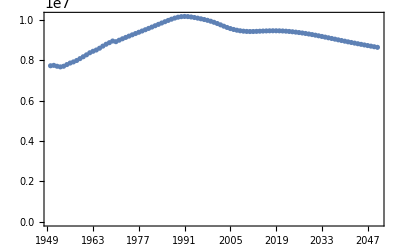

```mathematica
DateListPlot[ts,PlotRange->{{"1950","2050"},All},Joined->False]
```

С помощью функций TimeSeriesModelFit и TimeSeriesForecast сделаем предсказание на следующие 100 лет по имеющимся данным из базы знаний WolframAlpha

```mathematica
tsModel=TimeSeriesModelFit[ts];
tsForecast = TimeSeriesForecast[tsModel,{100}];
```

TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

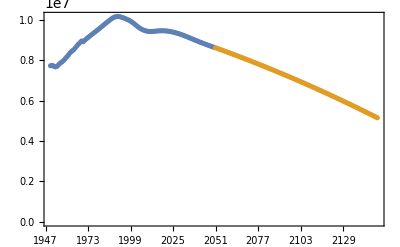

```mathematica
DateListPlot[{ts,tsForecast},PlotRange->{{"1950","2150"},All},Joined->False]
```

```mathematica
tsForecast["SliceData","2122"]
```

{6.24397×10^6 people}

```mathematica
MaltusModel[N0,t0,2122]/.{α[_]->α0,β[_]->β0}
NonLinearMaltus[α0/N0,β0,N0,t0,2122]
```

8.09688×10^6

7.06523×10^6

Вывод: как можно заметить из полученных данных, каждая из моделей выдает разный результат по численности населения Беларуси на 2122 год. Как же будет на самом деле, увидим в 2122 году :)

```mathematica
MaltusModel[N0,t0,t]/.{α[_]->α0,β[_]->β0}
```

9450233 ⅇ^(-0.001472 (-2017+t))

```mathematica
NonLinearMaltus[α0/N0,β0,N0,t0,t]
```

(1.00378×10^14)/(9450233+1.17153×10^6 ⅇ^(0.013346 (-2017+t)))

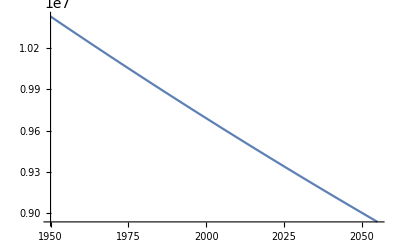

```mathematica
Plot[MaltusModel[N0,t0,t]/.{α[_]->α0,β[_]->β0},{t,1950,2055}]
```

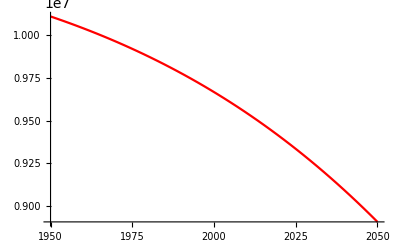

```mathematica
Plot[NonLinearMaltus[α0/N0,β0,N0,t0,t],{t,1950,2050},PlotStyle->Red]
```

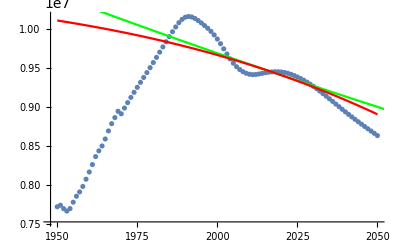

```mathematica
Show[ListPlot[Thread[{Range[1950,2050],peopleQuantityListBLR}]],
Plot[MaltusModel[N0,t0,t]/.{α[_]->α0,β[_]->β0},{t,1950,2130},PlotStyle->Green],
Plot[NonLinearMaltus[α0/N0,β0,N0,t0,t],{t,1950,2050},PlotStyle->Red]]
```

Вывод: как можно заметить из полученных данных графика, каждая из моделей выдает разный результат по численности населения Беларуси. Но стоит заметить, что модели Мальтуса и нелинейного Мальтуса получены из, практически, линейных графиков, в отличии от реальных данных. Также можно заметить, что 3 модели показали практически одинаковый результат на определенных промежутках времени. Однако, как говорится в известной всем пословице: “Раз в год и палка стреляет”. Обе модели Мальтуса являются плохо предсказуемыми, в принципе как и на основе данных Вольфрама, так как здесь не учитываются самые важные критерии долгожительности и прогноза численности населения, а также не учитываются те факторы, которые невозможно предугадать человеку и машине.

## Задание 5. Изменение численности населения страны. Определение параметров модели по реальным данным

По данным о численности населения для заданной страны в период с 1950 года до 2010 года найдите значения неизвестных параметров для
- модели Мальтуса с постоянными коэффициентами (см. Задание 1), 
- логистической модели (см. Задание 2) и 
- нелинейного аналоги модели Мальтуса (см. Задание 3), 
полагая, что t_0=1950 и N_0 являются известными. Для этого необходимо аппроксимировать реальные данные функциями аналитических решений для указанных моделей с помощью функции FindFit. 
Постройте графики относительной ошибки для найденных модельных решений в сравнении с реальными данными о численности населения.

Страны по вариантам:

Россия

Китай

Япония

Швеция

Франция

Греция

Марокко

Великобритания

Германия

Турция

Нидерланды

Бельгия

Катар

Египет

```mathematica
entitySweden = Entity["Country", "Sweden"];
```

```mathematica
{SN0, Sα0,Sβ0}=QuantityMagnitude@EntityValue[entitySweden,#]& /@{"Population","BirthRateFraction","DeathRateFraction"}
```

{10099270,0.012234,0.009107}

```mathematica
EntityValue[entitySweden,#,"Date"]& /@{"Population","BirthRateFraction","DeathRateFraction"}
```

{Year: 2020,Year: 2017,Year: 2017}

```mathematica
St0=2017;
```

```mathematica
SN0 = QuantityMagnitude@Dated[entitySweden, 2017]["Population"]
```

9904895

```mathematica
peopleQuantityListSWE=(Values@QuantityMagnitude@Dated[entitySweden,All]["Population"])⟦3;;⟧
%//Length
```

{1.7807×10^6,1.9252×10^6,2.0426×10^6,2.1183×10^6,2.1877×10^6,2.3473×10^6,2.3779×10^6,2.4651×10^6,2.5847×10^6,2.7713×10^6,2.8881×10^6,3.0254×10^6,3.1389×10^6,3.26×10^6,3.3165×10^6,3.4825×10^6,3.59×10^6,3.6393×10^6,3.8597×10^6,4.0226×10^6,4.1141×10^6,4.1685×10^6,4.298×10^6,4.4297×10^6,4.5657×10^6,4.6036×10^6,4.7172×10^6,4.785×10^6,4.8242×10^6,4.9626×10^6,5.1364×10^6,5.1752×10^6,5.1988×10^6,5.2213×10^6,5.2608×10^6,5.2949×10^6,5.3371×10^6,5.3777×10^6,5.4296×10^6,5.4764×10^6,5.5224×10^6,5.5618×10^6,5.6042×10^6,5.6386×10^6,5.6796×10^6,5.7127×10^6,5.7576×10^6,5.8008×10^6,5.8139×10^6,5.847×10^6,5.9045×10^6,5.9543×10^6,5.9875×10^6,6.0058×10^6,6.0361×10^6,6.0536×10^6,6.0744×10^6,6.0879×10^6,6.1×10^6,6.1201×10^6,6.1422×10^6,6.1624×10^6,6.1904×10^6,6.2116×10^6,6.2331×10^6,6.2505×10^6,6.2669×10^6,6.2847×10^6,6.3102×10^6,6.3413×10^6,6.3714×10^6,6.4065×10^6,6.4582×10^6,6.5228×10^6,6.56×10^6,6.674×10^6,6.7637×10^6,6.88×10^6,6.925×10^6,6.986×10^6,7.0418×10^6,7.099×10^6,7.151×10^6,7.192×10^6,7.235×10^6,7.262×10^6,7.316×10^6,7.367×10^6,7.415×10^6,7.454×10^6,7.498×10^6,7.52×10^6,7.5811×10^6,7.6275×10^6,7.6952×10^6,7.7725×10^6,7.8431×10^6,7.8928×10^6,7.935×10^6,8.0044×10^6,8054909,8095798,8127045,8151598,8173961,8197341,8223247,8250692,8277422,8299996,8316331,8325493,8329428,8332441,8340444,8357650,8384987,8421056,8464790,8514204,8567375,8625140,8686735,8746770,8798235,8836421,8859180,8868857,8870854,8873105,8881642,8897802,8920703,8951439,8990653,9038627,9096170,9162941,9236433,9313085,9390157,9466705,9542817,9618016,9692137,9764949,9836003,9904895,9971630,10036391,10099270,10160159,10218972,10275854,10331079,10384831,10437236,10488223,10537572,10584893,10629973,10672812,10713630,10752784,10790763,10827977,10864568,10900609,10936416,10972270,11008440,11045034,11082085,11119581,11157476,11195698,11234238,11273088,11312028,11350803,11389198}

181

```mathematica
Range[1950,2130]//Length
```

181

```mathematica
Sts = Dated[entitySweden, All]["Population"];
```

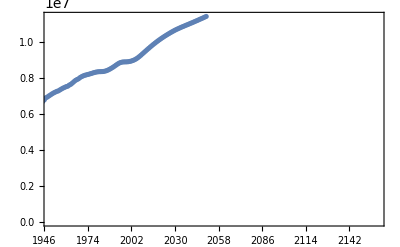

```mathematica
DateListPlot[Sts,PlotRange->{{"1950","2160"},All},Joined->False]
```

```mathematica
StsModel=TimeSeriesModelFit[Sts];
StsForecast = TimeSeriesForecast[StsModel,{100}];
```

TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

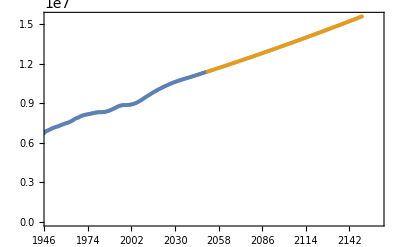

```mathematica
DateListPlot[{Sts,StsForecast},PlotRange->{{"1950","2160"},All},Joined->False]
```

```mathematica
StsForecast["SliceData","2122"]
```

{1.4344×10^7 people}

```mathematica
NonLinearMaltus[Sα0/SN0,Sβ0,SN0,St0,2122]
MaltusModel[SN0,St0,2122]/.{α[_]->Sα0,β[_]->Sβ0}
```

2.20121×10^7

1.37545×10^7

Вывод: как можно заметить из полученных данных, каждая из моделей выдает разный результат по численности населения Швеции на 2122 год. Но, если тщательно присмотреться, то мы можем заметить, что модель Мальтуса и модель, построенная из данных Вольфрама, практически выдают одни и те же прогнозы на 2122 год по численности населения. Как же будет на самом деле, увидим в 2122 году :)

```mathematica
MaltusModel[SN0,St0,t]/.{α[_]->Sα0,β[_]->Sβ0}
```

9904895 ⅇ^(0.003127 (-2017+t))

```mathematica
NonLinearMaltus[Sα0/SN0,Sβ0,SN0,St0,t]
```

(7.30309×10^13)/(9904895-2.53168×10^6 ⅇ^(0.009107 (-2017+t)))

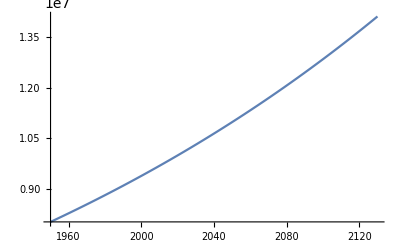

```mathematica
Plot[MaltusModel[SN0,St0,t]/.{α[_]->Sα0,β[_]->Sβ0},{t,1950,2130}]
```

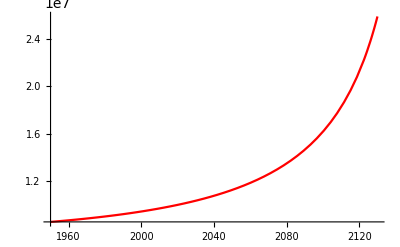

```mathematica
Plot[NonLinearMaltus[Sα0/SN0,Sβ0,SN0,St0,t],{t,1950,2130},PlotStyle->Red]
```

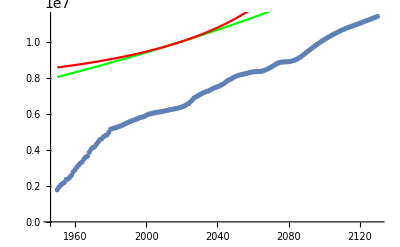

```mathematica
Show[ListPlot[Thread[{Range[1950,2130],peopleQuantityListSWE}]],
Plot[MaltusModel[SN0,St0,t]/.{α[_]->Sα0,β[_]->Sβ0},{t,1950,2130},PlotStyle->Green],
Plot[NonLinearMaltus[Sα0/SN0,Sβ0,SN0,St0,t],{t,1950,2130},PlotStyle->Red]]
```

Вывод: как можно заметить из полученных данных графика, каждая из моделей выдает разный результат по численности населения Швеции. Но стоит заметить, что модель Мальтуса получены из, практически, линейных графиков. Нелинейная модель Мальтуса получена из медленно растущей экспоненциального графика, в отличии от реальных данных. Также можно заметить, что модели Мальтуса показали практически одинаковый результат на определенных промежутках времени. Однако, как говорится в известной всем пословице: “Раз в год и палка стреляет”. Обе модели Мальтуса являются плохо предсказуемыми, в принципе как и на основе данных Вольфрама, так как здесь не учитываются самые важные критерии долгожительности и прогноза численности населения, а также не учитываются те факторы, которые невозможно предугадать человеку и машине.

#### Рекомендации по реализации

Воспользуемся данными из базы знаний Wolfram Alpha для Швеции

```mathematica
data ={ #,QuantityMagnitude@Dated[entitySweden, #]["Population"]}&  /@ Range[1950,2010];
```

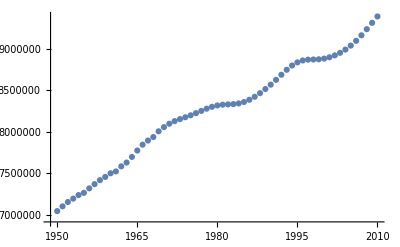

```mathematica
ListPlot[data]
```

Параметры модели t_0 и N_0 полагаем заданными

```mathematica
{t0,N0} = First@data
```

{1950,7.0418×10^6}

Найдем неизвестные параметры для модели Мальтуса с использованием функции FindFit

```mathematica
ClearAll[k,t]
```

```mathematica
solutionMalthus = N0 Exp[k(t-t0)];
```

```mathematica
FindFit[data,solutionMalthus ,{k},t]
```

{k→0.00491154}

Построим аналитическое решение для модели Мальтуса

```mathematica
solutionMalthus = solutionMalthus/.FindFit[data,solutionMalthus ,{k},t]
```

7.0418×10^6 ⅇ^(0.00491154 (-1950+t))

Построим график популяционной динамики на основании модели Мальтуса

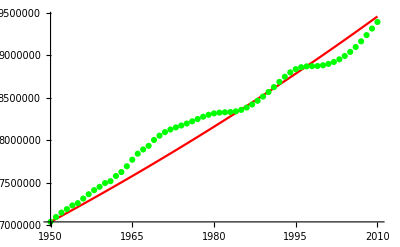

```mathematica
Show[Plot[solutionMalthus,{t,1950,2010}, PlotStyle->Red],ListPlot[data,PlotStyle->Green]]
```

Построим график относительной ошибки

```mathematica
errorMalthus = (Abs[Last@#-(solutionMalthus/.t->First@#) ]/Last@#)&/@data;
```

```mathematica
{Norm[errorMalthus],Norm[errorMalthus,Infinity]}
```

{0.139447,0.0356866}

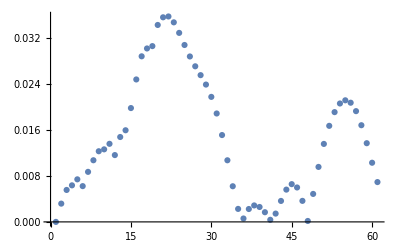

```mathematica
ListPlot[errorMalthus]
```

```mathematica
ClearAll[FindDataModel];
FindDataModel[model_,param_]:=Module[{sol,error,fitres},fitres=FindFit[data,model ,param,t];
sol=model/.fitres;
error=(Abs[Last@#-(sol/.t->First@#) ]/Last@#)&/@data;
Return[{fitres,sol,"NormError:",Norm[error],"NormError Infinity:",Norm[error,Infinity],
Show[ListPlot[data],Plot[sol,{t,1950,2010},PlotStyle->Green,PlotRange->All],PlotLabel->"Validation"],ListPlot[error,PlotLabel->"Error"]}]]
```

```mathematica
ClearAll[k,Np,α0,β0];
```

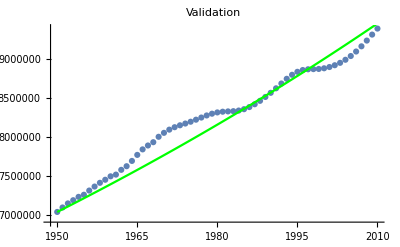
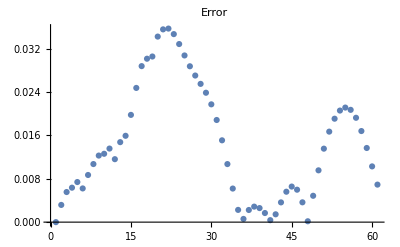
{{k→0.00491154},7.0418×10^6 ⅇ^(0.00491154 (-1950+t)),NormError:,0.139447,NormError Infinity:,0.0356866,-Graphics-,-Graphics-}

```mathematica
FindDataModel[N0 ⅇ^(k (t-t0)),{k}]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

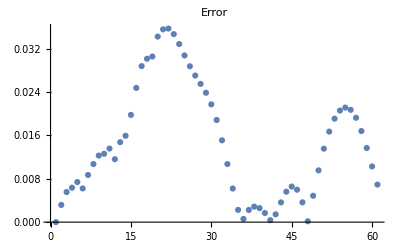
{{k→0.00491154,Np→-1.63877×10^13},-(1.15399×10^20 ⅇ^(0.00491154 (-1950+t)))/(-1.63877×10^13+7.0418×10^6 (-1+ⅇ^(0.00491154 (-1950+t)))),NormError:,0.139447,NormError Infinity:,0.0356866,-Graphics-,-Graphics-}

```mathematica
FindDataModel[(N0 Np ⅇ^(k(t-t0)))/(N0(ⅇ^(k (t-t0))-1)+Np),{k,Np}]
```

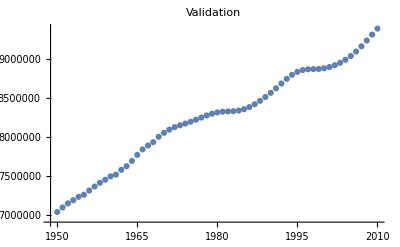
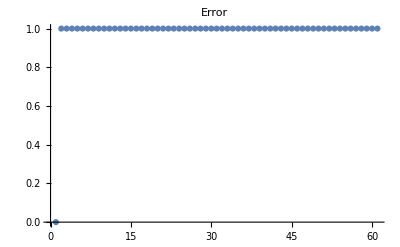
{{α0→73.0398,β0→142.88},(5.04463328275572×10^121010)/(2.57879355464873×10^121010-5.14331×10^8 ⅇ^(142.88 t)),NormError:,7.74597,NormError Infinity:,1.,-Graphics-,-Graphics-}

```mathematica
FindDataModel[(ⅇ^(t0 β0) N0 β0)/(-ⅇ^(t β0) N0 α0+ⅇ^(t0 β0) N0 α0+ⅇ^(t β0) β0),{α0,β0}](*здесь плохо отобразится график из-за того, что значение модели очень маленькое*)
```

```mathematica
FindDataModel[(β0/α0 N0)/(N0-(ⅇ^(β0 (t-t0)) (N0-β0/α0))),{α0,β0}](*здесь плохо отобразится график из-за того, что значение модели очень маленькое*)
```

General::munfl: 1.37752×10^7 (-7.790166844572×10^-318) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.37752×10^7 (-6.90864415785567×10^-380) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.37752×10^7 (-6.12687315331764×10^-442) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{α0→73.0398,β0→142.88},(1.37752×10^7)/(7.0418×10^6-7.0418×10^6 ⅇ^(142.88 (-1950+t))),NormError:,7.74597,NormError Infinity:,1.,-Graphics-,-Graphics-}

Вывод: как можно заметить из полученных данных графиков,  модель Мальтуса и Ферхюльста выдает практически один и тот же результат, что и результат, полученный из данных Вольфрама. Можно отметить, что графики относительной ошибки для найденных модельных решений Мальтуса и Ферхюльста показывают совсем незначительные ошибки, в отличии от модели нелинейного Мальтуса, так как полученные данные, почему-то (скорее всего из-за проблем с нормализацией данных для данной модели) выдают слишком маленькие результаты по численности населения.

## Задание 6. Рост численности населения Земли. Определение параметров модели по реальным данным

По данным о численности населения Земли, доступным из базы знаний Wolfram Alpha, найдите значения неизвестных параметров N_кр>0 и β_0>0 для нелинейного аналога модели Мальтуса (см. Задание 3), полагая, что t_0 и N_0 являются заданными. Для нахождения неизвестных параметров модели необходимо аппроксимировать реальные данные функцией аналитического решения с помощью функции FindFit, см. Задание 5.

В рамках нелинейного аналога модели Мальтуса найдите момент времени  t^*, при котором численность населения Земли примет бесконечное значение, т.е. lim_(t→t^*) N[t]=+∞, см. Задание 3.1.

Изобразите данные о численности населения Земли из базы знаний Wolfram Alpha, а также модельное решение на временном отрезке  [t_0,t^*].

Постройте график относительной ошибки для найденного модельного решения в сравнении с реальными данными о численности населения Земли, см. Задание 5.

#### Рекомендации по реализации

ВНИМАНИЕ!!! ACHTUNG!!!
НАЙДЕНА ПРОБЛЕМА С FINDFIT ПРИ ДАННЫХ dataWorld . ЕСЛИ ВЫ СМОЖЕТЕ ЭТО КАК - ТО ИСПРАВИТЬ, ТО ПРОСЬБА К ВАМ ВЫСЛАТЬ ПРАВИЛЬНЫЙ КОД, 
ЧТОБЫ УВИДЕТЬ РЕЗУЛЬТАТ 6 ЗАДАНИЯ :)

Воспользуемся данными из базы знаний Wolfram Alpha для населения Земли

```mathematica
entityWorld = Entity["Country", "World"];
```

```mathematica
dataWorld = Dated[entityWorld,All]["Population"];
```

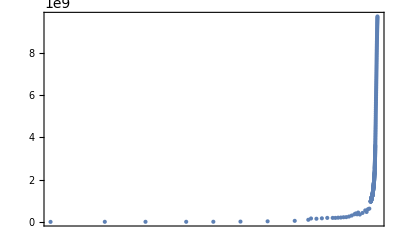

```mathematica
DateListPlot[dataWorld, Joined→False]
```

Параметры модели t_0 и N_0 полагаем заданными

```mathematica
{t0, N0} = {dataWorld["FirstDate"]⟦1,1⟧,dataWorld["FirstValue"]⟦1⟧}
```

{-10000,1.×10^6}

```mathematica
dataWorldBetter={First/@DateList/@dataWorld["Dates"],QuantityMagnitude[dataWorld["Values"]]}ᵀ;
```

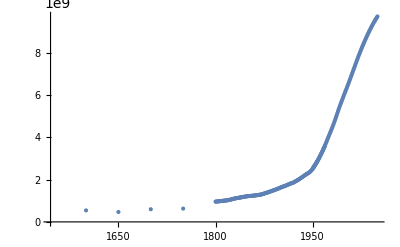

```mathematica
ListPlot[dataWorldBetter,Joined->False]
```

```mathematica
FindFit[dataWorldBetter,(Nkr N0)/(N0-(ⅇ^(β0 (t-t0)) (Nkr-N0))),{β0,Nkr},t]
```

FindFit::ivar: 1/2 is not a valid variable.

FindFit[{{-10000,1.×10^6},{-8000,5.×10^6},{-6500,5.×10^6},{-5000,5.×10^6},{-4000,7.×10^6},{-3000,1.4×10^7},{-2000,2.7×10^7},{-1000,5.×10^7},{-500,1.×10^8},{-400,1.62×10^8},{-200,1.5×10^8},{1,1.7×10^8},{200,1.9×10^8},{400,1.9×10^8},{500,1.9×10^8},{600,2.×10^8},{700,2.07×10^8},{800,2.2×10^8},{900,2.26×10^8},{1000,2.54×10^8},{1100,3.01×10^8},{1200,3.6×10^8},{1250,4.×10^8},{1300,3.6×10^8},{1340,4.43×10^8},{1400,3.5×10^8},{1500,4.25×10^8},{1600,5.45×10^8},{1650,4.7×10^8},{1700,6.×10^8},{1750,6.29×10^8},{1800,9.59398×10^8},{1801,9.62771×10^8},{1802,9.66178×10^8},{1803,9.69588×10^8},{1804,9.73012×10^8},{1805,9.76467×10^8},{1806,9.79932×10^8},{1807,9.83396×10^8},{1808,9.86847×10^8},{1809,9.90288×10^8},{1810,9.93729×10^8},{1811,9.97294×10^8},{1812,1.00086×10^9},{1813,1.00443×10^9},{1814,1.008×10^9},{1815,1.01157×10^9},{1816,1.01519×10^9},{1817,1.0196×10^9},{1818,1.02402×10^9},{1819,1.02844×10^9},{1820,1.03289×10^9},{1821,1.04042×10^9},{1822,1.04807×10^9},{1823,1.0558×10^9},{1824,1.06374×10^9},{1825,1.07172×10^9},{1826,1.07951×10^9},{1827,1.08731×10^9},{1828,1.09519×10^9},{1829,1.1042×10^9},{1830,1.11332×10^9},{1831,1.11825×10^9},{1832,1.12308×10^9},{1833,1.12788×10^9},{1834,1.1326×10^9},{1835,1.13819×10^9},{1836,1.14377×10^9},{1837,1.14934×10^9},{1838,1.15527×10^9},{1839,1.16113×10^9},{1840,1.16706×10^9},{1841,1.17234×10^9},{1842,1.17772×10^9},{1843,1.1831×10^9},{1844,1.18859×10^9},{1845,1.19418×10^9},{1846,1.1997×10^9},{1847,1.20545×10^9},{1848,1.21081×10^9},{1849,1.21642×10^9},{1850,1.22222×10^9},{1851,1.22314×10^9},{1852,1.22437×10^9},{1853,1.22707×10^9},{1854,1.22982×10^9},{1855,1.23252×10^9},{1856,1.23535×10^9},{1857,1.23889×10^9},{1858,1.24213×10^9},{1859,1.24594×10^9},{1860,1.24982×10^9},{1861,1.25442×10^9},{1862,1.25782×10^9},{1863,1.26252×10^9},{1864,1.26664×10^9},{1865,1.27096×10^9},{1866,1.27507×10^9},{1867,1.27936×10^9},{1868,1.28415×10^9},{1869,1.28973×10^9},{1870,1.29454×10^9},{1871,1.3041×10^9},{1872,1.31308×10^9},{1873,1.3224×10^9},{1874,1.332×10^9},{1875,1.34305×10^9},{1876,1.35174×10^9},{1877,1.36299×10^9},{1878,1.37291×10^9},{1879,1.38232×10^9},{1880,1.39238×10^9},{1881,1.4033×10^9},{1882,1.41357×10^9},{1883,1.42435×10^9},{1884,1.43523×10^9},{1885,1.44633×10^9},{1886,1.45656×10^9},{1887,1.46719×10^9},{1888,1.4779×10^9},{1889,1.48891×10^9},{1890,1.50015×10^9},{1891,1.51123×10^9},{1892,1.52259×10^9},{1893,1.5343×10^9},{1894,1.54651×10^9},{1895,1.55859×10^9},{1896,1.56995×10^9},{1897,1.58305×10^9},{1898,1.59565×10^9},{1899,1.60838×10^9},{1900,1.62213×10^9},{1901,1.63426×10^9},{1902,1.64836×10^9},{1903,1.65931×10^9},{1904,1.66993×10^9},{1905,1.68118×10^9},{1906,1.69166×10^9},{1907,1.70325×10^9},{1908,1.71541×10^9},{1909,1.72705×10^9},{1910,1.73973×10^9},{1911,1.75433×10^9},{1912,1.76818×10^9},{1913,1.78183×10^9},{1914,1.7948×10^9},{1915,1.80717×10^9},{1916,1.81933×10^9},{1917,1.83066×10^9},{1918,1.83914×10^9},{1919,1.8462×10^9},{1920,1.863×10^9},{1921,1.8777×10^9},{1922,1.8955×10^9},{1923,1.91341×10^9},{1924,1.93141×10^9},{1925,1.94955×10^9},{1926,1.96526×10^9},{1927,1.9823×10^9},{1928,2.0022×10^9},{1929,2.02117×10^9},{1930,2.04218×10^9},{1931,2.06252×10^9},{1932,2.08547×10^9},{1933,2.10693×10^9},{1934,2.12708×10^9},{1935,2.14843×10^9},{1936,2.16973×10^9},{1937,2.19175×10^9},{1938,2.21398×10^9},{1939,2.23624×10^9},{1940,2.25517×10^9},{1941,2.2733×10^9},{1942,2.29303×10^9},{1943,2.31105×10^9},{1944,2.33046×10^9},{1945,2.35258×10^9},{1946,2.37847×10^9},{1947,2.40986×10^9},{1948,2.44143×10^9},{1949,2.47313×10^9},{1950,2.51679×10^9},{1950,2536431018},{1951,2.55959×10^9},{1951,2584034227},{1952,2.60516×10^9},{1952,2630861690},{1953,2.65191×10^9},{1953,2677609061},{1954,2.70184×10^9},{1954,2724846754},{1955,2.75663×10^9},{1955,2773019915},{1956,2.80276×10^9},{1956,2822443254},{1957,2.85836×10^9},{1957,2873306058},{1958,2.91433×10^9},{1958,2925686680},{1959,2.9725×10^9},{1959,2979576147},{1960,3.03284×10^9},{1960,3034949715},{1961,3.09419×10^9},{1961,3091843513},{1962,3.16074×10^9},{1962,3150420761},{1963,3.22435×10^9},{1963,3211000946},{1964,3.28876×10^9},{1964,3273978272},{1965,3.35431×10^9},{1965,3339583510},{1966,3.41662×10^9},{1966,3407922631},{1967,3.48201×10^9},{1967,3478770104},{1968,3.54795×10^9},{1968,3551599436},{1969,3.61517×10^9},{1969,3625680965},{1970,3700437042},{1971,3775760030},{1972,3851650588},{1973,3927780519},{1974,4003794178},{1975,4079480474},{1976,4154666827},{1977,4229505919},{1978,4304533599},{1979,4380506185},{1980,4458003466},{1981,4536996619},{1982,4617386526},{1983,4699569187},{1984,4784011517},{1985,4870921666},{1986,4960568000},{1987,5052521998},{1988,5145425994},{1989,5237441434},{1990,5327231041},{1991,5414289383},{1992,5498919893},{1993,5581597598},{1994,5663150428},{1995,5744212930},{1996,5824891931},{1997,5905045647},{1998,5984794075},{1999,6064239033},{2000,6143493806},{2001,6222626531},{2002,6301773172},{2003,6381185141},{2004,6461159391},{2005,6541906956},{2006,6623517917},{2007,6705946643},{2008,6789088672},{2009,6872766988},{2010,6956823588},{2011,7041194168},{2012,7125827957},{2013,7210582041},{2014,7295290759},{2015,7379796967},{2016,7464021934},{2017,7547858900},{2018,7631091113},{2019,7713468205},{2020,7794798729},{2021,7874965732},{2022,7953952577},{2023,8031800338},{2024,8108605255},{2025,8184437453},{2026,8259276651},{2027,8333078318},{2028,8405863301},{2029,8477660723},{2030,8548487371},{2031,8618349454},{2032,8687227873},{2033,8755083512},{2034,8821862705},{2035,8887524229},{2036,8952048885},{2037,9015437616},{2038,9077693645},{2039,9138828562},{2040,9198847382},{2041,9257745483},{2042,9315508153},{2043,9372118247},{2044,9427555382},{2045,9481803272},{2046,9534854673},{2047,9586707749},{2048,9637357320},{2049,9686800146},{2050,9735033900}},500000./(1.×10^6+1.×10^6 ⅇ^((10000+t) β0)),{β0,1/2},t]

```mathematica
FindFit[dataWorldBetter,(ⅇ^(t0 β0) N0 Nkr)/(ⅇ^(t0 β0) N0+ⅇ^(t β0)(Nkr- N0)) ,{β0,Nkr},t]
```

FindFit::ivar: 1/2 is not a valid variable.

FindFit[{{-10000,1.×10^6},{-8000,5.×10^6},{-6500,5.×10^6},{-5000,5.×10^6},{-4000,7.×10^6},{-3000,1.4×10^7},{-2000,2.7×10^7},{-1000,5.×10^7},{-500,1.×10^8},{-400,1.62×10^8},{-200,1.5×10^8},{1,1.7×10^8},{200,1.9×10^8},{400,1.9×10^8},{500,1.9×10^8},{600,2.×10^8},{700,2.07×10^8},{800,2.2×10^8},{900,2.26×10^8},{1000,2.54×10^8},{1100,3.01×10^8},{1200,3.6×10^8},{1250,4.×10^8},{1300,3.6×10^8},{1340,4.43×10^8},{1400,3.5×10^8},{1500,4.25×10^8},{1600,5.45×10^8},{1650,4.7×10^8},{1700,6.×10^8},{1750,6.29×10^8},{1800,9.59398×10^8},{1801,9.62771×10^8},{1802,9.66178×10^8},{1803,9.69588×10^8},{1804,9.73012×10^8},{1805,9.76467×10^8},{1806,9.79932×10^8},{1807,9.83396×10^8},{1808,9.86847×10^8},{1809,9.90288×10^8},{1810,9.93729×10^8},{1811,9.97294×10^8},{1812,1.00086×10^9},{1813,1.00443×10^9},{1814,1.008×10^9},{1815,1.01157×10^9},{1816,1.01519×10^9},{1817,1.0196×10^9},{1818,1.02402×10^9},{1819,1.02844×10^9},{1820,1.03289×10^9},{1821,1.04042×10^9},{1822,1.04807×10^9},{1823,1.0558×10^9},{1824,1.06374×10^9},{1825,1.07172×10^9},{1826,1.07951×10^9},{1827,1.08731×10^9},{1828,1.09519×10^9},{1829,1.1042×10^9},{1830,1.11332×10^9},{1831,1.11825×10^9},{1832,1.12308×10^9},{1833,1.12788×10^9},{1834,1.1326×10^9},{1835,1.13819×10^9},{1836,1.14377×10^9},{1837,1.14934×10^9},{1838,1.15527×10^9},{1839,1.16113×10^9},{1840,1.16706×10^9},{1841,1.17234×10^9},{1842,1.17772×10^9},{1843,1.1831×10^9},{1844,1.18859×10^9},{1845,1.19418×10^9},{1846,1.1997×10^9},{1847,1.20545×10^9},{1848,1.21081×10^9},{1849,1.21642×10^9},{1850,1.22222×10^9},{1851,1.22314×10^9},{1852,1.22437×10^9},{1853,1.22707×10^9},{1854,1.22982×10^9},{1855,1.23252×10^9},{1856,1.23535×10^9},{1857,1.23889×10^9},{1858,1.24213×10^9},{1859,1.24594×10^9},{1860,1.24982×10^9},{1861,1.25442×10^9},{1862,1.25782×10^9},{1863,1.26252×10^9},{1864,1.26664×10^9},{1865,1.27096×10^9},{1866,1.27507×10^9},{1867,1.27936×10^9},{1868,1.28415×10^9},{1869,1.28973×10^9},{1870,1.29454×10^9},{1871,1.3041×10^9},{1872,1.31308×10^9},{1873,1.3224×10^9},{1874,1.332×10^9},{1875,1.34305×10^9},{1876,1.35174×10^9},{1877,1.36299×10^9},{1878,1.37291×10^9},{1879,1.38232×10^9},{1880,1.39238×10^9},{1881,1.4033×10^9},{1882,1.41357×10^9},{1883,1.42435×10^9},{1884,1.43523×10^9},{1885,1.44633×10^9},{1886,1.45656×10^9},{1887,1.46719×10^9},{1888,1.4779×10^9},{1889,1.48891×10^9},{1890,1.50015×10^9},{1891,1.51123×10^9},{1892,1.52259×10^9},{1893,1.5343×10^9},{1894,1.54651×10^9},{1895,1.55859×10^9},{1896,1.56995×10^9},{1897,1.58305×10^9},{1898,1.59565×10^9},{1899,1.60838×10^9},{1900,1.62213×10^9},{1901,1.63426×10^9},{1902,1.64836×10^9},{1903,1.65931×10^9},{1904,1.66993×10^9},{1905,1.68118×10^9},{1906,1.69166×10^9},{1907,1.70325×10^9},{1908,1.71541×10^9},{1909,1.72705×10^9},{1910,1.73973×10^9},{1911,1.75433×10^9},{1912,1.76818×10^9},{1913,1.78183×10^9},{1914,1.7948×10^9},{1915,1.80717×10^9},{1916,1.81933×10^9},{1917,1.83066×10^9},{1918,1.83914×10^9},{1919,1.8462×10^9},{1920,1.863×10^9},{1921,1.8777×10^9},{1922,1.8955×10^9},{1923,1.91341×10^9},{1924,1.93141×10^9},{1925,1.94955×10^9},{1926,1.96526×10^9},{1927,1.9823×10^9},{1928,2.0022×10^9},{1929,2.02117×10^9},{1930,2.04218×10^9},{1931,2.06252×10^9},{1932,2.08547×10^9},{1933,2.10693×10^9},{1934,2.12708×10^9},{1935,2.14843×10^9},{1936,2.16973×10^9},{1937,2.19175×10^9},{1938,2.21398×10^9},{1939,2.23624×10^9},{1940,2.25517×10^9},{1941,2.2733×10^9},{1942,2.29303×10^9},{1943,2.31105×10^9},{1944,2.33046×10^9},{1945,2.35258×10^9},{1946,2.37847×10^9},{1947,2.40986×10^9},{1948,2.44143×10^9},{1949,2.47313×10^9},{1950,2.51679×10^9},{1950,2536431018},{1951,2.55959×10^9},{1951,2584034227},{1952,2.60516×10^9},{1952,2630861690},{1953,2.65191×10^9},{1953,2677609061},{1954,2.70184×10^9},{1954,2724846754},{1955,2.75663×10^9},{1955,2773019915},{1956,2.80276×10^9},{1956,2822443254},{1957,2.85836×10^9},{1957,2873306058},{1958,2.91433×10^9},{1958,2925686680},{1959,2.9725×10^9},{1959,2979576147},{1960,3.03284×10^9},{1960,3034949715},{1961,3.09419×10^9},{1961,3091843513},{1962,3.16074×10^9},{1962,3150420761},{1963,3.22435×10^9},{1963,3211000946},{1964,3.28876×10^9},{1964,3273978272},{1965,3.35431×10^9},{1965,3339583510},{1966,3.41662×10^9},{1966,3407922631},{1967,3.48201×10^9},{1967,3478770104},{1968,3.54795×10^9},{1968,3551599436},{1969,3.61517×10^9},{1969,3625680965},{1970,3700437042},{1971,3775760030},{1972,3851650588},{1973,3927780519},{1974,4003794178},{1975,4079480474},{1976,4154666827},{1977,4229505919},{1978,4304533599},{1979,4380506185},{1980,4458003466},{1981,4536996619},{1982,4617386526},{1983,4699569187},{1984,4784011517},{1985,4870921666},{1986,4960568000},{1987,5052521998},{1988,5145425994},{1989,5237441434},{1990,5327231041},{1991,5414289383},{1992,5498919893},{1993,5581597598},{1994,5663150428},{1995,5744212930},{1996,5824891931},{1997,5905045647},{1998,5984794075},{1999,6064239033},{2000,6143493806},{2001,6222626531},{2002,6301773172},{2003,6381185141},{2004,6461159391},{2005,6541906956},{2006,6623517917},{2007,6705946643},{2008,6789088672},{2009,6872766988},{2010,6956823588},{2011,7041194168},{2012,7125827957},{2013,7210582041},{2014,7295290759},{2015,7379796967},{2016,7464021934},{2017,7547858900},{2018,7631091113},{2019,7713468205},{2020,7794798729},{2021,7874965732},{2022,7953952577},{2023,8031800338},{2024,8108605255},{2025,8184437453},{2026,8259276651},{2027,8333078318},{2028,8405863301},{2029,8477660723},{2030,8548487371},{2031,8618349454},{2032,8687227873},{2033,8755083512},{2034,8821862705},{2035,8887524229},{2036,8952048885},{2037,9015437616},{2038,9077693645},{2039,9138828562},{2040,9198847382},{2041,9257745483},{2042,9315508153},{2043,9372118247},{2044,9427555382},{2045,9481803272},{2046,9534854673},{2047,9586707749},{2048,9637357320},{2049,9686800146},{2050,9735033900}},(500000. ⅇ^(-10000 β0))/(1.×10^6 ⅇ^(-10000 β0)-1.×10^6 ⅇ^(t β0)),{β0,1/2},t]

```mathematica
FindFit[dataWorldBetter,(ⅇ^(t0 β0) N0 β0)/(-ⅇ^(t β0) N0 α0+ⅇ^(t0 β0) N0 α0+ⅇ^(t β0) β0) ,{α0,β0},t]
```

General::munfl: Exp[-10000.] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindFit::nrlnum: The function value {Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,-1.×10^8,-1.62×10^8,«292»} is not a list of real numbers with dimensions {302} at {α0,β0} = {1.,1.}.

FindFit[{{-10000,1.×10^6},{-8000,5.×10^6},{-6500,5.×10^6},{-5000,5.×10^6},{-4000,7.×10^6},{-3000,1.4×10^7},{-2000,2.7×10^7},{-1000,5.×10^7},{-500,1.×10^8},{-400,1.62×10^8},{-200,1.5×10^8},{1,1.7×10^8},{200,1.9×10^8},{400,1.9×10^8},{500,1.9×10^8},{600,2.×10^8},{700,2.07×10^8},{800,2.2×10^8},{900,2.26×10^8},{1000,2.54×10^8},{1100,3.01×10^8},{1200,3.6×10^8},{1250,4.×10^8},{1300,3.6×10^8},{1340,4.43×10^8},{1400,3.5×10^8},{1500,4.25×10^8},{1600,5.45×10^8},{1650,4.7×10^8},{1700,6.×10^8},{1750,6.29×10^8},{1800,9.59398×10^8},{1801,9.62771×10^8},{1802,9.66178×10^8},{1803,9.69588×10^8},{1804,9.73012×10^8},{1805,9.76467×10^8},{1806,9.79932×10^8},{1807,9.83396×10^8},{1808,9.86847×10^8},{1809,9.90288×10^8},{1810,9.93729×10^8},{1811,9.97294×10^8},{1812,1.00086×10^9},{1813,1.00443×10^9},{1814,1.008×10^9},{1815,1.01157×10^9},{1816,1.01519×10^9},{1817,1.0196×10^9},{1818,1.02402×10^9},{1819,1.02844×10^9},{1820,1.03289×10^9},{1821,1.04042×10^9},{1822,1.04807×10^9},{1823,1.0558×10^9},{1824,1.06374×10^9},{1825,1.07172×10^9},{1826,1.07951×10^9},{1827,1.08731×10^9},{1828,1.09519×10^9},{1829,1.1042×10^9},{1830,1.11332×10^9},{1831,1.11825×10^9},{1832,1.12308×10^9},{1833,1.12788×10^9},{1834,1.1326×10^9},{1835,1.13819×10^9},{1836,1.14377×10^9},{1837,1.14934×10^9},{1838,1.15527×10^9},{1839,1.16113×10^9},{1840,1.16706×10^9},{1841,1.17234×10^9},{1842,1.17772×10^9},{1843,1.1831×10^9},{1844,1.18859×10^9},{1845,1.19418×10^9},{1846,1.1997×10^9},{1847,1.20545×10^9},{1848,1.21081×10^9},{1849,1.21642×10^9},{1850,1.22222×10^9},{1851,1.22314×10^9},{1852,1.22437×10^9},{1853,1.22707×10^9},{1854,1.22982×10^9},{1855,1.23252×10^9},{1856,1.23535×10^9},{1857,1.23889×10^9},{1858,1.24213×10^9},{1859,1.24594×10^9},{1860,1.24982×10^9},{1861,1.25442×10^9},{1862,1.25782×10^9},{1863,1.26252×10^9},{1864,1.26664×10^9},{1865,1.27096×10^9},{1866,1.27507×10^9},{1867,1.27936×10^9},{1868,1.28415×10^9},{1869,1.28973×10^9},{1870,1.29454×10^9},{1871,1.3041×10^9},{1872,1.31308×10^9},{1873,1.3224×10^9},{1874,1.332×10^9},{1875,1.34305×10^9},{1876,1.35174×10^9},{1877,1.36299×10^9},{1878,1.37291×10^9},{1879,1.38232×10^9},{1880,1.39238×10^9},{1881,1.4033×10^9},{1882,1.41357×10^9},{1883,1.42435×10^9},{1884,1.43523×10^9},{1885,1.44633×10^9},{1886,1.45656×10^9},{1887,1.46719×10^9},{1888,1.4779×10^9},{1889,1.48891×10^9},{1890,1.50015×10^9},{1891,1.51123×10^9},{1892,1.52259×10^9},{1893,1.5343×10^9},{1894,1.54651×10^9},{1895,1.55859×10^9},{1896,1.56995×10^9},{1897,1.58305×10^9},{1898,1.59565×10^9},{1899,1.60838×10^9},{1900,1.62213×10^9},{1901,1.63426×10^9},{1902,1.64836×10^9},{1903,1.65931×10^9},{1904,1.66993×10^9},{1905,1.68118×10^9},{1906,1.69166×10^9},{1907,1.70325×10^9},{1908,1.71541×10^9},{1909,1.72705×10^9},{1910,1.73973×10^9},{1911,1.75433×10^9},{1912,1.76818×10^9},{1913,1.78183×10^9},{1914,1.7948×10^9},{1915,1.80717×10^9},{1916,1.81933×10^9},{1917,1.83066×10^9},{1918,1.83914×10^9},{1919,1.8462×10^9},{1920,1.863×10^9},{1921,1.8777×10^9},{1922,1.8955×10^9},{1923,1.91341×10^9},{1924,1.93141×10^9},{1925,1.94955×10^9},{1926,1.96526×10^9},{1927,1.9823×10^9},{1928,2.0022×10^9},{1929,2.02117×10^9},{1930,2.04218×10^9},{1931,2.06252×10^9},{1932,2.08547×10^9},{1933,2.10693×10^9},{1934,2.12708×10^9},{1935,2.14843×10^9},{1936,2.16973×10^9},{1937,2.19175×10^9},{1938,2.21398×10^9},{1939,2.23624×10^9},{1940,2.25517×10^9},{1941,2.2733×10^9},{1942,2.29303×10^9},{1943,2.31105×10^9},{1944,2.33046×10^9},{1945,2.35258×10^9},{1946,2.37847×10^9},{1947,2.40986×10^9},{1948,2.44143×10^9},{1949,2.47313×10^9},{1950,2.51679×10^9},{1950,2536431018},{1951,2.55959×10^9},{1951,2584034227},{1952,2.60516×10^9},{1952,2630861690},{1953,2.65191×10^9},{1953,2677609061},{1954,2.70184×10^9},{1954,2724846754},{1955,2.75663×10^9},{1955,2773019915},{1956,2.80276×10^9},{1956,2822443254},{1957,2.85836×10^9},{1957,2873306058},{1958,2.91433×10^9},{1958,2925686680},{1959,2.9725×10^9},{1959,2979576147},{1960,3.03284×10^9},{1960,3034949715},{1961,3.09419×10^9},{1961,3091843513},{1962,3.16074×10^9},{1962,3150420761},{1963,3.22435×10^9},{1963,3211000946},{1964,3.28876×10^9},{1964,3273978272},{1965,3.35431×10^9},{1965,3339583510},{1966,3.41662×10^9},{1966,3407922631},{1967,3.48201×10^9},{1967,3478770104},{1968,3.54795×10^9},{1968,3551599436},{1969,3.61517×10^9},{1969,3625680965},{1970,3700437042},{1971,3775760030},{1972,3851650588},{1973,3927780519},{1974,4003794178},{1975,4079480474},{1976,4154666827},{1977,4229505919},{1978,4304533599},{1979,4380506185},{1980,4458003466},{1981,4536996619},{1982,4617386526},{1983,4699569187},{1984,4784011517},{1985,4870921666},{1986,4960568000},{1987,5052521998},{1988,5145425994},{1989,5237441434},{1990,5327231041},{1991,5414289383},{1992,5498919893},{1993,5581597598},{1994,5663150428},{1995,5744212930},{1996,5824891931},{1997,5905045647},{1998,5984794075},{1999,6064239033},{2000,6143493806},{2001,6222626531},{2002,6301773172},{2003,6381185141},{2004,6461159391},{2005,6541906956},{2006,6623517917},{2007,6705946643},{2008,6789088672},{2009,6872766988},{2010,6956823588},{2011,7041194168},{2012,7125827957},{2013,7210582041},{2014,7295290759},{2015,7379796967},{2016,7464021934},{2017,7547858900},{2018,7631091113},{2019,7713468205},{2020,7794798729},{2021,7874965732},{2022,7953952577},{2023,8031800338},{2024,8108605255},{2025,8184437453},{2026,8259276651},{2027,8333078318},{2028,8405863301},{2029,8477660723},{2030,8548487371},{2031,8618349454},{2032,8687227873},{2033,8755083512},{2034,8821862705},{2035,8887524229},{2036,8952048885},{2037,9015437616},{2038,9077693645},{2039,9138828562},{2040,9198847382},{2041,9257745483},{2042,9315508153},{2043,9372118247},{2044,9427555382},{2045,9481803272},{2046,9534854673},{2047,9586707749},{2048,9637357320},{2049,9686800146},{2050,9735033900}},(1.×10^6 ⅇ^(-10000 β0) β0)/(1.×10^6 ⅇ^(-10000 β0) α0-1.×10^6 ⅇ^(t β0) α0+ⅇ^(t β0) β0),{α0,β0},t]

```mathematica
ClearAll[FindDataModelWorld,β0,Nkr];
FindDataModelWorld[model_,param_]:=Module[{sol,error,fitres,tStar,Nkr},fitres=FindFit[dataWorldBetter,model ,param,t];
sol=model/.fitres;
error=(Abs[Last@#-(sol/.t->First@#) ]/Last@#)&/@dataWorldBetter;
Return[{fitres,sol,"NormError:",Norm[error],"NormError Infinity:",Norm[error,Infinity],"t^*:",tStar=Log[N0/(N0-fitres⟦2,2⟧)]/fitres⟦1,2⟧+t0,
Show[ListPlot[dataWorld],Plot[sol,{t,t0,2050},PlotStyle->Green],PlotLabel->"Validation"],ListPlot[error,PlotLabel->"Error"]}]]
```

General::munfl: 1.×10^6 2.5765384494996×10^-875 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.×10^6 9.31780833583035×10^-1527 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.×10^6 3.36969751800644×10^-2178 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

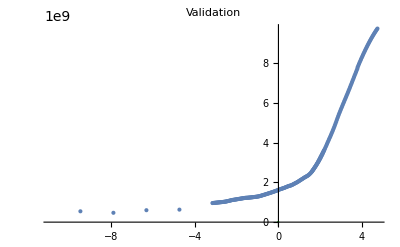
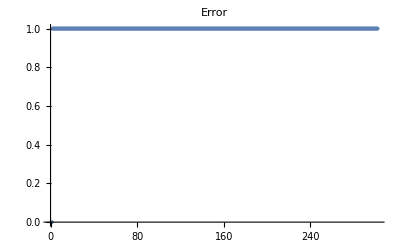
{{β0→1.,Nkr→1.×10^6},(1.×10^12)/(1.×10^6-3.77277 ⅇ^(1. (10000+t))),NormError:,17.3494,NormError Infinity:,1.,t^*:,-9987.51+3.14159 ⅈ,-Graphics-,-Graphics-}

```mathematica
FindDataModelWorld[(Nkr N0)/(N0-(ⅇ^(β0 (t-t0)) (Nkr-N0))),{β0,Nkr}]
```

```mathematica
(*FindDataModelWorld[(ⅇ^(t0 β0) N0 β0)/(-ⅇ^(t β0) N0 α0+ⅇ^(t0 β0) N0 α0+ⅇ^(t β0) β0),{α0,β0}]
					||
					||
FindDataModelWorld[(ⅇ^(t0 β0) N0 Nkr)/(ⅇ^(t0 β0) N0+ⅇ^(t β0)(Nkr- N0)),{β0,Nkr}] - данные модели были посчитаны при помощи DSolve, после преобразования к переменным β0 и Nkr данные вообще не просчитываются. Проблема кроется в функции FindFit, которая не может посчитать при заданных данных dataWorld. Как можно заметить, *)
```

```mathematica
(*ниже приведенный код просто показывает, что происходит с данными dataWorld при моедли Мальтуса и Ферхюльста*)
ClearAll[FindDataModelWorldMalFerh];
FindDataModelWorldMalFerh[model_,param_]:=Module[{sol,error,fitres,tStar,Nkr},fitres=FindFit[dataWorldBetter,model ,param,t];
sol=model/.fitres;
error=(Abs[Last@#-(sol/.t->First@#) ]/Last@#)&/@dataWorldBetter;
Return[{fitres,sol,"NormError:",Norm[error],"NormError Infinity:",Norm[error,Infinity],
Show[ListPlot[dataWorld],Plot[sol,{t,t0,2050},PlotStyle->Green],PlotLabel->"Validation"],ListPlot[error,PlotLabel->"Error"]}]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ListPlot::prng: Value of option PlotRange -> {{0.,302.},{0,1.10530686654761×10^5164}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

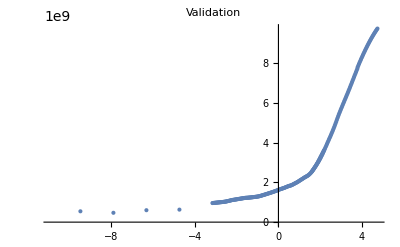
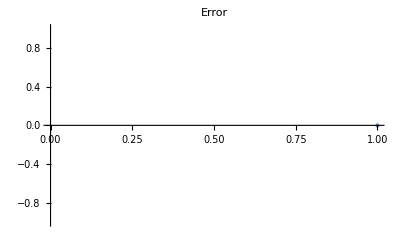
{{k→0.991701},1.×10^6 ⅇ^(0.991701 (10000+t)),NormError:,7.28862140540968×10^5185,NormError Infinity:,6.76319357823806×10^5185,-Graphics-,-Graphics-}

```mathematica
FindDataModelWorldMalFerh[N0 ⅇ^(k (t-t0)),{k}]
```

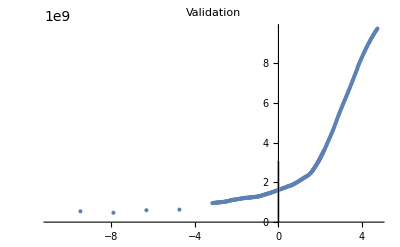
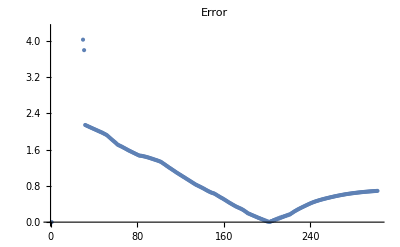
{{k→1.,Np→3.01671×10^9},(3.01671×10^15 ⅇ^(1. (10000+t)))/(3.01671×10^9+1.×10^6 (-1+ⅇ^(1. (10000+t)))),NormError:,1157.2,NormError Infinity:,602.341,-Graphics-,-Graphics-}

```mathematica
FindDataModelWorldMalFerh[(N0 Np ⅇ^(k(t-t0)))/(N0(ⅇ^(k (t-t0))-1)+Np),{k,Np}]
```

## Задание 7* (необязательное). Математическая модель радиоактивного распада

Постройте математическую модель радиоактивного распада вещества по аналогии с моделью Мальтуса. Сделайте предположение, что скорость распада радиоактивного вещества пропорционален количеству этого вещества x=x(t), где коэффициент пропорциональности является постоянным k=const<0. Для информации смотрите [5, c. 18]. 

Используя вид аналитического решения математической модели в виде задачи Коши с начальным условием x(t)=x_0 определите, как связан коэффициент пропорциональности k со временем T полураспада радиоактивного вещества: x(T)=x_0/2? 

Дополнительно решите задачу 2.7 и задачу 2.8 из [5, с.18].

## Задание 8* (необязательное). Математическая модель распространения нового продукта на рынке

Данное задание является примером построения и анализа математической модели в экономике.

Постройте математическую модель распространения нового продукта или услуги на рынке (модель Басса). В качестве неизвестной величины рассматривается количество пользователей некоторого продукта или услуги N(t) на рынке. Используя принцип аналогии полагается, что за счет рекламы скорость изменения пользователей N'(t) пропорциональна числу потенциальных клиентов N_0-N(t), где N_0 -- общее количество людей на рынке. Дополнительно учитывается эффект косвенной рекламы за счет общения пользователей продукта с потенциальными клиентами. Для информации смотрите [1, c. 150]. 

Анализируя математическую модель, определите момент времени, начиная с которого продолжать рекламу становится невыгодным. Для информации смотрите [1, c. 150].

## Литература

[1] А. А. Самарский, А. П. Михайлов. Математическое моделирование: Идеи. Методы. Примеры. -- М.: Физматлит, 2001.

[2] А. С. Братусь, А. С. Новожилов, А. П. Платонов. Динамические системы и модели биологии. -- 2011.

[3] Д. Мюррей. Математическая биология. Том I. Введение. -- М.-Ижевск, 2009.

[4] B. Barnes and G. R. Fulford. Mathematical Modelling with Case Studies: A differential equation approach using Maple and MATLAB. Second Edition. -- CRC Press, 2008.

[5] Р. А. Прохорова. Обыкновенные дифференциальные уравнения : учебное пособие. -- Мн. : БГУ, 2017. http://elib.bsu.by/handle/123456789/205697

[6] В. В. Амелькин. Дифференциальные уравнения : учебное пособие. -- Мн. : БГУ, 2012. http://elib.bsu.by/handle/123456789/43871